# Integrations for Inertia

An example to follow for Robotics

### Load the vector tools and the basic integrand for the inertia matrix

Vector tools

```mathematica
<<"/Users/alanbarhorst/Book/Rev2010/dynmath/math3/vectors3"
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

Inertia matrix integrand.

```mathematica
Ip[r1_,r2_,r3_]:={{r2^2 + r3^2, - r1 r2, -r1 r3},{-r2 r1, r1^2 + r3^2, -r2 r3},{-r3 r1, -r3 r2, r1^2 + r2^2}}
```

```mathematica
MatrixForm[Ip[r1,r2,r3]]
```

(r2^2+r3^2 | -r1 r2 | -r1 r3
-r1 r2 | r1^2+r3^2 | -r2 r3
-r1 r3 | -r2 r3 | r1^2+r2^2)

### Problem 1: Conical Shell

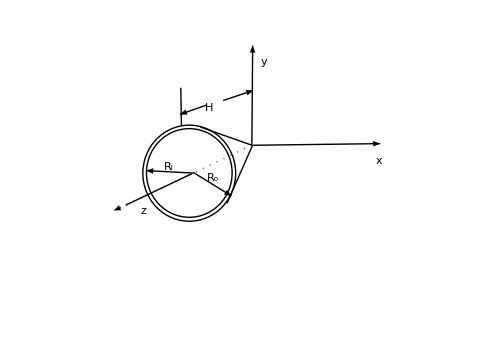

This model has simple geometry

```mathematica
b[x_]:=unitVector[B,b,x]
```

```mathematica
b[1]
```

(b̂)_1

In this body a cylindical coordinate system system is present (r, θ, z). 

Ri = inside radius
Ro = outside radius
H = height in 3-direction
ρ = mass density

Here is the position vector to every mass point with respect to the body origin

```mathematica
BrP = r (Cos[θ] b[1] + Sin[θ] b[2])  + z b[3]//distributeScalars//gatherVectors
```

r Cos[θ] (b̂)_1+r Sin[θ] (b̂)_2+z (b̂)_3

Here it is as a function for use in the integration

```mathematica
rf[r_,θ_,z_]={BrP.b[1],BrP.b[2],BrP.b[3]}
```

{r Cos[θ],r Sin[θ],z}

The cone lines  have the following geometry

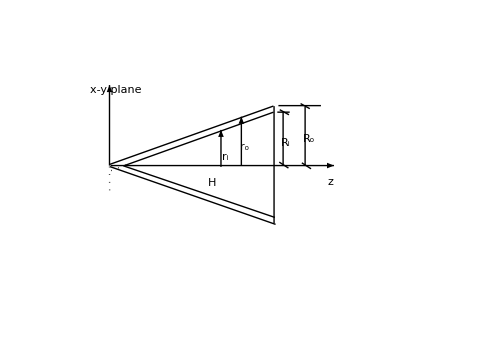

By similar triangles we see that

```mathematica
ro[Ro_,Ri_,H_,z_]:=(Ro/H)z
```

And we need to turn off the inner cone function after z gets smaller than where the inner cone crosses z = 0

```mathematica
ri[Ro_,Ri_,H_,z_]:=Piecewise[{{(Ro/H )z - (Ro-Ri),z≥H(Ro-Ri)/Ro}},0]
```

Here is a picture

```mathematica
Manipulate[
Show[
{ParametricPlot3D[rf[r,θ,H],{r,ri[Ro,Ri,H,H],ro[Ro,Ri,H,H]},{θ,0,2Pi}],ParametricPlot3D[{rf[ro[Ro,Ri,H,z],θ,z],rf[ri[Ro,Ri,H,z],θ,z]},{z,0.001,H},{θ,0,2 Pi}]},PlotRange->{{-Ro,Ro},{-Ro,Ro},{0,H}},ViewVertical->{0,1,0},ViewPoint->{H,H,H},AxesLabel->{"x","y","z"}],{{Ri,.45},0.001,5},{{Ro,.5},.01,5},{{H,1},.01,5}]
```

Here is the volume calculation.  The assumptions makes the integrator’s work easier

```mathematica
$Assumptions={Ro>0,Ri>0,H>0,Ro>Ri,ρ>0}
```

{Ro>0,Ri>0,H>0,Ro>Ri,ρ>0}

```mathematica
Vol=∫_0^(2Pi) ∫_0^H ∫_ri[Ro,Ri,H,z]^ro[Ro,Ri,H,z] rⅆrⅆzⅆθ//Simplify
```

(H π (-Ri^3+Ro^3))/(3 Ro)

Here is the total mass calculation

```mathematica
Mass=∫_0^(2Pi) ∫_0^H ∫_ri[Ro,Ri,H,z]^ro[Ro,Ri,H,z] (ρ )rⅆrⅆzⅆθ//Simplify
```

(H π (-Ri^3+Ro^3) ρ)/(3 Ro)

Here is the center of mass location

```mathematica
CMass=(1/Mass∫_0^(2Pi) ∫_0^H ∫_ri[Ro,Ri,H,z]^ro[Ro,Ri,H,z] ( ρ rf[r,θ,z])rⅆrⅆzⅆθ)//Simplify
```

{0,0,(H (Ri^4-4 Ri^3 Ro+3 Ro^4))/(4 (-Ri^3 Ro+Ro^4))}

If the cone is thin then Ri -> Ro, the mass center is

```mathematica
Limit[CMass,Ri->Ro]/.{Ro->R}
```

{0,0,(2 H)/3}

Here is the inertia matrix, written in terms of mass not density

```mathematica
IMat=(∫_0^(2Pi) ∫_0^H ∫_ri[Ro,Ri,H,z]^ro[Ro,Ri,H,z] ( ρ Ip[rf[r,θ,z][[1]],rf[r,θ,z][[2]],rf[r,θ,z][[3]]])rⅆrⅆzⅆθ)//.ρ->(M/Vol)//Simplify
```

{{(M (3 Ro^2 (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4)+2 H^2 (Ri^4-4 Ri^3 Ro+6 Ri^2 Ro^2+6 Ri Ro^3+6 Ro^4)))/(20 Ro^2 (Ri^2+Ri Ro+Ro^2)),0,0},{0,(M (3 Ro^2 (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4)+2 H^2 (Ri^4-4 Ri^3 Ro+6 Ri^2 Ro^2+6 Ri Ro^3+6 Ro^4)))/(20 Ro^2 (Ri^2+Ri Ro+Ro^2)),0},{0,0,(3 M (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4))/(10 (Ri^2+Ri Ro+Ro^2))}}

```mathematica
MatrixForm[IMat]
```

((M (3 Ro^2 (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4)+2 H^2 (Ri^4-4 Ri^3 Ro+6 Ri^2 Ro^2+6 Ri Ro^3+6 Ro^4)))/(20 Ro^2 (Ri^2+Ri Ro+Ro^2)) | 0 | 0
0 | (M (3 Ro^2 (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4)+2 H^2 (Ri^4-4 Ri^3 Ro+6 Ri^2 Ro^2+6 Ri Ro^3+6 Ro^4)))/(20 Ro^2 (Ri^2+Ri Ro+Ro^2)) | 0
0 | 0 | (3 M (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4))/(10 (Ri^2+Ri Ro+Ro^2)))

If the cone is thin then Ri -> Ro

```mathematica
MatrixForm[IMat/.{Ri->Ro}/.{Ro->R}//Expand]
```

((H^2 M)/2+(M R^2)/4 | 0 | 0
0 | (H^2 M)/2+(M R^2)/4 | 0
0 | 0 | (M R^2)/2)

Here is what the ineria dyadic looks like

```mathematica
bb[x_,y_]:=unitDyad[b[x],b[y]]
```

```mathematica
IDyad=Sum[IMat[[i]][[j]] bb[i,j],{i,1,3},{j,1,3}]/.{Ri->Ro}/.{Ro->R}//Simplify
```

1/4 M ((2 H^2+R^2) ((b̂)_1(b̂)_1)+(2 H^2+R^2) ((b̂)_2(b̂)_2)+2 R^2 ((b̂)_3(b̂)_3))

### Problem 2: Hyperboloid of Two Sheets

In this body the height is a spatial curve given in the problems statement.  
L =1/2 length of shape in 1-direction
W =1/2 width of shape in 2-direction
H = 1/2 height in 3-direction, determined by zTop[L,0,a,b,c] 
ρ = mass density

Solving for z=z[x,y] gives

```mathematica
zTop[x_,y_,a_,b_,c_]:=(c^2(1+x^2/a^2 + y^2/b^2))^1/2
```

Here is a plot of the shape with the variable boundaries.

```mathematica
Manipulate[Plot3D[{-zTop[x,y,a,b,c],zTop[x,y,a,b,c]},{x,-L,L},{y,-W,W},PlotRange->{{-L,L},{-W,W},{-zTop[L,0,a,b,c],zTop[L,0,a,b,c]}},AxesLabel->{"x","y","z"}],{{a,.13},.01,1,Appearance->"Open"},{{b,.16},.01,1,Appearance->"Open"},{{c,.1},.01,1,Appearance->"Open"},{{L,.2},.01,1,Appearance->"Open"},{{W,.24},.01,1,Appearance->"Open"}]
```

Here is the postition out to each mass point

```mathematica
BrP = x b[1] +y b[2]+ z b[3]
```

x (b̂)_1+y (b̂)_2+z (b̂)_3

Here are some numbers to set the geometry and mass

```mathematica
r[x_,y_,z_]={BrP.b[1],BrP.b[2],BrP.b[3]}
```

{x,y,z}

The first lower limit bounds the bottom to the values of the curve at the saddle edges

```mathematica
$Assumptions={a>0,b>0,c>0,W>0,L>0}
```

{a>0,b>0,c>0,W>0,L>0}

```mathematica
Vol=∫_-W^W ∫_-L^L ∫_(-zTop[x,y,a,b,c])^zTop[x,y,a,b,c] ⅆzⅆxⅆy
```

4/3 c^2 L W (3+L^2/a^2+W^2/b^2)

Here is the mass

```mathematica
Mass=∫_-W^W ∫_-L^L ∫_(-zTop[x,y,a,b,c])^zTop[x,y,a,b,c] ρⅆzⅆxⅆy
```

(4 c^2 L W (b^2 L^2+a^2 (3 b^2+W^2)) ρ)/(3 a^2 b^2)

Here is the center of mass

```mathematica
CMass=(1/Mass∫_-W^W ∫_-L^L ∫_(-zTop[x,y,a,b,c])^zTop[x,y,a,b,c] ρ r[x,y,z]ⅆzⅆxⅆy)
```

{0,0,0}

Here is the inertia matrix in term of mass not density

```mathematica
IMat=(∫_-W^W ∫_-L^L ∫_(-zTop[x,y,a,b,c])^zTop[x,y,a,b,c] (ρ Ip[x,y,z])ⅆzⅆxⅆy)//.ρ->(M/Vol)//Simplify
```

{{1/(420 a^6 b^6 (3+L^2/a^2+W^2/b^2))M (15 b^6 c^4 L^6+21 a^2 b^4 c^4 L^4 (3 b^2+W^2)+7 a^4 b^2 L^2 (10 b^2 c^4 W^2+3 c^4 W^4+5 b^4 (3 c^4+4 W^2))+3 a^6 (21 b^2 c^4 W^4+5 c^4 W^6+35 b^6 (c^4+4 W^2)+7 b^4 (5 c^4 W^2+12 W^4))),0,0},{0,1/(420 a^6 b^6 (3+L^2/a^2+W^2/b^2))M (15 b^6 c^4 L^6+21 a^2 b^4 c^4 L^4 (3 b^2+W^2)+7 a^4 b^2 L^2 (3 b^4 (5 c^4+12 L^2)+10 b^2 c^4 W^2+3 c^4 W^4)+a^6 (105 b^6 (c^4+4 L^2)+35 b^4 (3 c^4+4 L^2) W^2+63 b^2 c^4 W^4+15 c^4 W^6)),0},{0,0,(M (b^2 L^2 (9 L^2+5 W^2)+a^2 (5 L^2 W^2+9 W^4+15 b^2 (L^2+W^2))))/(15 (b^2 L^2+a^2 (3 b^2+W^2)))}}

```mathematica
MatrixForm[IMat]
```

((M (15 b^6 c^4 L^6+21 a^2 b^4 c^4 L^4 (3 b^2+W^2)+7 a^4 b^2 L^2 (10 b^2 c^4 W^2+3 c^4 W^4+5 b^4 (3 c^4+4 W^2))+3 a^6 (21 b^2 c^4 W^4+5 c^4 W^6+35 b^6 (c^4+4 W^2)+7 b^4 (5 c^4 W^2+12 W^4))))/(420 a^6 b^6 (3+L^2/a^2+W^2/b^2)) | 0 | 0
0 | (M (15 b^6 c^4 L^6+21 a^2 b^4 c^4 L^4 (3 b^2+W^2)+7 a^4 b^2 L^2 (3 b^4 (5 c^4+12 L^2)+10 b^2 c^4 W^2+3 c^4 W^4)+a^6 (105 b^6 (c^4+4 L^2)+35 b^4 (3 c^4+4 L^2) W^2+63 b^2 c^4 W^4+15 c^4 W^6)))/(420 a^6 b^6 (3+L^2/a^2+W^2/b^2)) | 0
0 | 0 | (M (b^2 L^2 (9 L^2+5 W^2)+a^2 (5 L^2 W^2+9 W^4+15 b^2 (L^2+W^2))))/(15 (b^2 L^2+a^2 (3 b^2+W^2))))

Here is the dyadic form of the inertia

```mathematica
bb[x_,y_]:=unitDyad[b[x],b[y]]
```

```mathematica
IDyad=Sum[IMat[[i]][[j]] bb[i,j],{i,1,3},{j,1,3}]//Chop
```

1/(420 a^6 b^6 (3+L^2/a^2+W^2/b^2))M (15 b^6 c^4 L^6+21 a^2 b^4 c^4 L^4 (3 b^2+W^2)+7 a^4 b^2 L^2 (10 b^2 c^4 W^2+3 c^4 W^4+5 b^4 (3 c^4+4 W^2))+3 a^6 (21 b^2 c^4 W^4+5 c^4 W^6+35 b^6 (c^4+4 W^2)+7 b^4 (5 c^4 W^2+12 W^4))) ((b̂)_1(b̂)_1)+1/(420 a^6 b^6 (3+L^2/a^2+W^2/b^2))M (15 b^6 c^4 L^6+21 a^2 b^4 c^4 L^4 (3 b^2+W^2)+7 a^4 b^2 L^2 (3 b^4 (5 c^4+12 L^2)+10 b^2 c^4 W^2+3 c^4 W^4)+a^6 (105 b^6 (c^4+4 L^2)+35 b^4 (3 c^4+4 L^2) W^2+63 b^2 c^4 W^4+15 c^4 W^6)) ((b̂)_2(b̂)_2)+(M (b^2 L^2 (9 L^2+5 W^2)+a^2 (5 L^2 W^2+9 W^4+15 b^2 (L^2+W^2))) ((b̂)_3(b̂)_3))/(15 (b^2 L^2+a^2 (3 b^2+W^2)))

### Problem 3: Asymmetric I-Beam

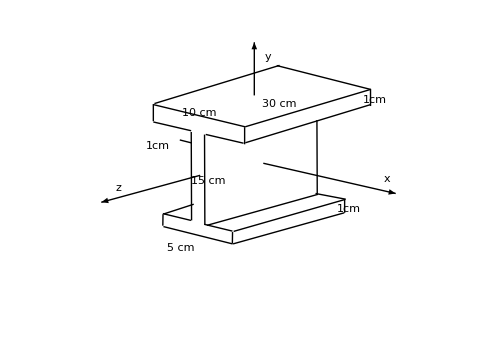

This model has piecewise geometry, or the problems can be worked by combining simple shapes.

```mathematica
b[x_]:=unitVector[B,b,x]
```

```mathematica
b[1]
```

(b̂)_1

In this body a tappered beam system is present.  
L = full length of beam in 3-direction, 30 cm
T = thickness of beam webbing, 1 cm
H = in 2-direction, (15 + 2) cm
Wb = beam base width in 1-direction, 5 cm
Wt = beam top width in 1-direction, 10 cm

ρ = mass density

Here is the position out to each mass point

```mathematica
BrP = x b[1] +y b[2]+ z b[3]
```

x (b̂)_1+y (b̂)_2+z (b̂)_3

```mathematica
r[x_,y_,z_]={BrP.b[1],BrP.b[2],BrP.b[3]}
```

{x,y,z}

Function for top on along the x direction, the back side will just mirror this

```mathematica
xTop[y_,H_,Wb_,Wt_,T_]=Piecewise[{{Wb,-H/2≤  y<-H/2+T},{T/2,-H/2+T≤  y< H/2-T},{Wt,H/2-T≤ y<H/2}},0]
```

Piecewise[{{Wb, -H/2≤y<-H/2+T}, {T/2, -H/2+T≤y<H/2-T}, {Wt, H/2-T≤y<H/2}, {0, True}}]

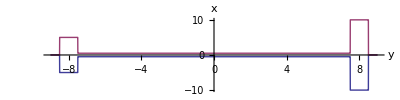

```mathematica
Plot[{-xTop[y,17,5,10,1],xTop[y,17,5,10,1]},{y,-18/2,18/2},AxesLabel->{"y","x"},Exclusions->None,PlotRange->All,AspectRatio->1/4]
```

```mathematica
Plot3D[{-xTop[y,17,5,10,1],xTop[y,17,5,10,1]},{y,-17/1.99,17/1.99},{z,-15.1,15.1},
PlotRange->{{-10,10},{-15,15},{-17/2,17/2}},Exclusions->None,PlotPoints->100,AxesLabel->{"y","z","x"},ViewVertical->{1,0,0},ViewPoint->{0,1,.75}]
```

-Graphics3D-

Set Constants m and kg for steel

```mathematica
L=30./100;
H=17./100;
Wb=5./100;
Wt=10./100;
T=1./100;
ρ=7750. ;(*kg/m^3*)
```

Here is the volume (m^3)

```mathematica
Vol=∫_(-H/2)^(H/2) ∫_(-xTop[y,H,Wb,Wt,T])^xTop[y,H,Wb,Wt,T] ∫_(-L/2)^(L/2) ⅆzⅆxⅆy
```

0.00135

Here is the mass (kg)

```mathematica
Mass=∫_(-H/2)^(H/2) ∫_(-xTop[y,H,Wb,Wt,T])^xTop[y,H,Wb,Wt,T] ∫_(-L/2)^(L/2) ρⅆzⅆxⅆy
```

10.4625

Here is the center of mass (m)

```mathematica
CMass=(1/Mass∫_(-H/2)^(H/2) ∫_(-xTop[y,H,Wb,Wt,T])^xTop[y,H,Wb,Wt,T] ∫_(-L/2)^(L/2) ρ r[x,y,z]ⅆzⅆxⅆy)
```

{0.,0.0177778,0.}

Here is the inertia matrix (kg m^2)

```mathematica
IMat=(∫_(-H/2)^(H/2) ∫_(-xTop[y,H,Wb,Wt,T])^xTop[y,H,Wb,Wt,T] ∫_(-L/2)^(L/2) (ρ Ip[x,y,z])ⅆzⅆxⅆy)
```

{{0.129706,0.,0.},{0.,0.0959353,0.},{0.,0.,0.0687037}}

```mathematica
MatrixForm[IMat]
```

(0.129706 | 0. | 0.
0. | 0.0959353 | 0.
0. | 0. | 0.0687037)

Here is the dyadic form of the inertia (kg m^2)

```mathematica
bb[x_,y_]:=unitDyad[b[x],b[y]]
```

```mathematica
IDyad=Sum[IMat[[i]][[j]] bb[i,j],{i,1,3},{j,1,3}]//Chop
```

0.129706 ((b̂)_1(b̂)_1)+0.0959353 ((b̂)_2(b̂)_2)+0.0687037 ((b̂)_3(b̂)_3)

### Problem 4: Radii of gyration

The radii of gyration simply define the major moments of inertia as follows. M=25 slug, k1=0.5 ft, k2=0.5 ft k3=2 ft.

```mathematica
bb[x_,y_]:=unitDyad[b[x],b[y]]
```

```mathematica
m=.
```

```mathematica
M=20 slug
k1=0.5ft
k2=0.5 ft
k3=2ft
```

20 slug

0.5 ft

0.5 ft

2 ft

```mathematica
IDyad=M (k1^2 bb[1,1] + k2^2 bb[2,2] + k3^2 bb[3,3])//Expand
```

5. ft^2 slug ((b̂)_1(b̂)_1)+5. ft^2 slug ((b̂)_2(b̂)_2)+80 ft^2 slug ((b̂)_3(b̂)_3)

Basic shape sketch is same down the 1-axis and the 2-axis, and really spread about the 3-axis.  A thin large diameter disk.